# Лабораторная 2. Списки и матрицы

Сохраните настоящий файл на СВОЕЙ флешке или в СВОЕМ Home, под своей фамилией с номером 2. Например, Ivanov2.nb.

Задание 1.  Чем отличаются команды MatrixForm, TableForm и Grid? Посмотрите Help и сделайте эксперименты.

Задание 2.  С помощью команд Prime и Table составьте список первых 100 простых чисел.  С помощью команды Part найдите 15-ое простое число.   С помощью команды Position найдите порядковый номер простого числа 127.

```mathematica
primes = Table[Prime[n], {n, 100}]

primes[[15]]

Position[primes, 127]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541}

47

{{31}}

```mathematica
prime=Table[Prime[i],{i,100}]
prime[[15]]
Position[prime,127]
%[[1,1]]
```

Задание 3. Создайте список {3, 5, 7, 9, 11} с помощью команды Range. Создайте диагональную матрицу, на диагонали которой стоят перечисленные числа (команда DiagonalMatrix).

```mathematica
range = Range[3, 11, 2]

diagonalMatrix = DiagonalMatrix[range]

MatrixForm[diagonalMatrix]
TableForm[diagonalMatrix]
Grid[diagonalMatrix]
```

{3,5,7,9,11}

{{3,0,0,0,0},{0,5,0,0,0},{0,0,7,0,0},{0,0,0,9,0},{0,0,0,0,11}}

(3 | 0 | 0 | 0 | 0
0 | 5 | 0 | 0 | 0
0 | 0 | 7 | 0 | 0
0 | 0 | 0 | 9 | 0
0 | 0 | 0 | 0 | 11)

3 | 0 | 0 | 0 | 0
0 | 5 | 0 | 0 | 0
0 | 0 | 7 | 0 | 0
0 | 0 | 0 | 9 | 0
0 | 0 | 0 | 0 | 11

3 | 0 | 0 | 0 | 0
0 | 5 | 0 | 0 | 0
0 | 0 | 7 | 0 | 0
0 | 0 | 0 | 9 | 0
0 | 0 | 0 | 0 | 11

```mathematica
d=Range[3,11,2]
a=DiagonalMatrix[d];
MatrixForm[a]
```

Задание 4. Напишите команду prepend0, дописывающую к каждому списку впереди и сзади ноль (используйте Append и Prepend  или AppendTo и PrependTo).

```mathematica
list = Range[1, 5]
Prepend[Append[list, 0], 0]
```

{1,2,3,4,5}

{0,1,2,3,4,5,0}

```mathematica
perpend0[a_List]:=Append[Prepend[a,0],0]
perpend0[{1,3}] (*Проверка*)
```

Задание 5. Чем отличаются возможности команд ListPlot и DiscretePlot? Изобразите множество точек (n, sin n/10), когда n меняется от 0 до 50.

{0,Sin[1/10],Sin[1/5],Sin[3/10],Sin[2/5],Sin[1/2],Sin[3/5],Sin[7/10],Sin[4/5],Sin[9/10],Sin[1],Sin[11/10],Sin[6/5],Sin[13/10],Sin[7/5],Sin[3/2],Sin[8/5],Sin[17/10],Sin[9/5],Sin[19/10],Sin[2],Sin[21/10],Sin[11/5],Sin[23/10],Sin[12/5],Sin[5/2],Sin[13/5],Sin[27/10],Sin[14/5],Sin[29/10],Sin[3],Sin[31/10],Sin[16/5],Sin[33/10],Sin[17/5],Sin[7/2],Sin[18/5],Sin[37/10],Sin[19/5],Sin[39/10],Sin[4],Sin[41/10],Sin[21/5],Sin[43/10],Sin[22/5],Sin[9/2],Sin[23/5],Sin[47/10],Sin[24/5],Sin[49/10],Sin[5]}

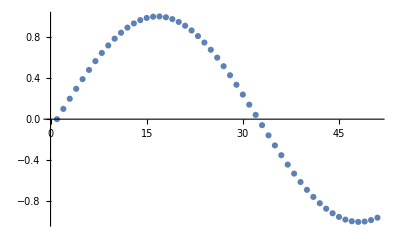

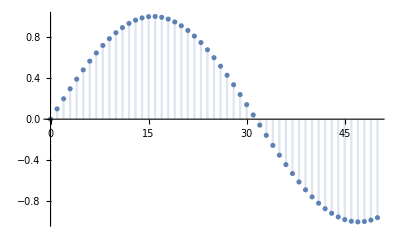

```mathematica
nums = Table[Sin[n / 10], {n, 0, 50}]
ListPlot[nums]
DiscretePlot[Sin[n / 10], {n, 0, 50}]
```

```mathematica
"ListPlot изображает график функции,заданной таблично,а DiscretePlot изображает график функции,заданной аналитически на множестве целых чисел."

DiscretePlot[Sin[n/10],{n,0,50}]
```

Задание 6. Создайте список f[3], f[4], ..., f[11] с помощью команды Array.  Преобразуйте этот список в сумму f[3]+f[4]+...+f[11] с помощью команды Apply. Указание. См. Help.

```mathematica
Array[f, 9, {3, 11}]
Apply[Plus, Array[f, 9, {3, 11}]]
Plus @@ Array[f, 9, {3, 11}]
```

{f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10],f[11]}

f[3]+f[4]+f[5]+f[6]+f[7]+f[8]+f[9]+f[10]+f[11]

f[3]+f[4]+f[5]+f[6]+f[7]+f[8]+f[9]+f[10]+f[11]

```mathematica
a=Array[f,5,{3,11}]
Apply[Plus,a]
```

Задание 7. Напишите программу, превращающую целое число 255629 в список его цифр {2,5,5,6,2,9}. УКАЗАНИЕ . Используйте команды FractionalPart , IntegerPart , Reverse , Log10 , Table . Ср. с работой команд IntegerDigits и RealDigits.

```mathematica
num = 255629
fracPart = FractionalPart[num / (10 ^ n)]
Table[fracPart, {n, 1, Ceiling[Log10[num]]}] 
Table[IntegerPart[fracPart], {n, 1, Ceiling[Log10[num]]}] 
Table[IntegerPart[fracPart * 10], {n, 1, Ceiling[Log10[num]]}] 
IntegerDigits[num]
RealDigits[num]
```

255629

FractionalPart[255629 10^-n]

{9/10,29/100,629/1000,5629/10000,55629/100000,255629/1000000}

{0,0,0,0,0,0}

{9,2,6,5,5,2}

{2,5,5,6,2,9}

{{2,5,5,6,2,9},6}

Задание 8. Составьте программу, превращающую список натуральных чисел в True, если в нем есть простые числа, и в False в противном случае (используйте команды PrimeQ, Apply, Or).

```mathematica
primes = Table[Prime[n], {n, 5}]
others = Select[Range[10], !PrimeQ[#]&]

Apply[Or, PrimeQ[primes]]
Apply[Or, PrimeQ[others]]
```

{2,3,5,7,11}

{1,4,6,8,9,10}

True

False

255629

FractionalPart[255629 10^-n]

{9/10,29/100,629/1000,5629/10000,55629/100000,255629/1000000}

{0,0,0,0,0,0}

{9,2,6,5,5,2}

{2,5,5,6,2,9}

{{2,5,5,6,2,9},6}

```mathematica
n=7;
list=Table[RandomInteger[10000],{n}]
z=PrimeQ[list]
Apply[Or,z]
```

Задание 9. Напишите программу, вычисляющую угол между заданными векторами (используйте команду Norm ).

```mathematica
length = 2
firstVector = Table[Random[], {length}]
secondVector = Table[Random[], {length}]
Dot[firstVector, secondVector] / (Norm[firstVector] * Norm[secondVector])
```

2

{0.122422,0.0322889}

{0.0730024,0.105303}

0.760488

```mathematica
n=5;
a=Table[Random[],{n}]
b=Table[Random[],{n}]
a.b/(Norm[a]*Norm[b])//ArcCos
```

Задание 10. Найдите наибольшее отрицательное число в заданном списке (используйте команды Select , Negative , Max ).

```mathematica
list = {7, 9, -1, -4, 5, -22}
Select[list, Negative]
Max[Select[list, Negative]]
```

{7,9,-1,-4,5,-22}

{-1,-4,-22}

-1

```mathematica
n=7;
list=Table[Random[],{n}]-1/2
Select[list,Negative]
%//Max
```

Задание 11. Дана матрица и строка (столбец).Вставьте строку (столбец) на k-ое место (команды Insert и Transpose).

```mathematica
n = 5;
pos = 1;
m = Table[2 * i + 1, {i, n}, {j, n}];
MatrixForm[m]
line = Range[1, 5]
newM = Insert[m, line, pos];
MatrixForm[newM]
```

(3 | 3 | 3 | 3 | 3
5 | 5 | 5 | 5 | 5
7 | 7 | 7 | 7 | 7
9 | 9 | 9 | 9 | 9
11 | 11 | 11 | 11 | 11)

{1,2,3,4,5}

(1 | 2 | 3 | 4 | 5
3 | 3 | 3 | 3 | 3
5 | 5 | 5 | 5 | 5
7 | 7 | 7 | 7 | 7
9 | 9 | 9 | 9 | 9
11 | 11 | 11 | 11 | 11)

```mathematica
n=3;k=2;
a=DiagonalMatrix[Range@n];
MatrixForm[a]
b=Table[Random[],{n}]
c=Insert[a,b,2];
MatrixForm[c]
d=Transpose[Insert[Transpose[a] a,b,2]];
MatrixForm[d]
```

Задание 12.Для n = 4 создайте матрицу размера n×n, состоящую из (одних и тех же) чисел 3 (команда Table или ConstantArray). Замените (команды Part и Do) в ней наддиагональные элементы на случайные числа из отрезка[0, 10] (команда Random), имеющие две значащие цифры после запятой (команда NumberForm) Выведите окончательный результат на экран командой MatrixForm. А как поменять поддиагональные элементы? Сделайте то же самое для n = 5.

```mathematica
n=4;
d=ConstantArray[3,{n,n}]
Do[d[[i,j]]=NumberForm[Random[]*10,{3,2}],{i,n-1},{j,i+1,n}];
MatrixForm[d]
d1=ConstantArray[3,{n,n}]
Do[d1[[i,j]]=NumberForm[Random[]*10,{3,2}],{j,n-1},{i,j+1,n}];
MatrixForm[d1]
```

```mathematica
n = 4;
m = ConstantArray[3, {n, n}];
MatrixForm[m]
Do[m[[i,j]] = NumberForm[RandomReal[{0,10}],{3,2}], {i, n - 1}, {j, i + 1, n}];
Do[m[[i,j]] = NumberForm[RandomReal[{0,10}],{3,2}], {i, 2, n}, {j, 1, i - 1}];
MatrixForm[m]
```

(3 | 3 | 3 | 3
3 | 3 | 3 | 3
3 | 3 | 3 | 3
3 | 3 | 3 | 3)

(3 | 6.21 | 5.80 | 6.29
1.58 | 3 | 6.30 | 0.08
2.77 | 6.50 | 3 | 8.21
3.66 | 6.75 | 6.60 | 3)